```mathematica
vmax=11;
p=0.1;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.1,0.001];
dmax=Round[rho*1.2,0.001];
dd=Round[(dmax-dmin)/22,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<20,i++;
Print[dmin+i*dd]
]
For[i=1,i<4,i++;
Print[i*rho]
]
```

0.076  :Transition density!!!

0.008 : Min density

0.091 : Max density

0.004 : density step

List of simulated values:

0.008

0.012

0.016

0.02

0.024

0.028

0.032

0.036

0.04

0.044

0.048

0.052

0.056

0.06

0.064

0.068

0.072

0.076

0.08

0.084

0.088

0.152

0.228

0.304

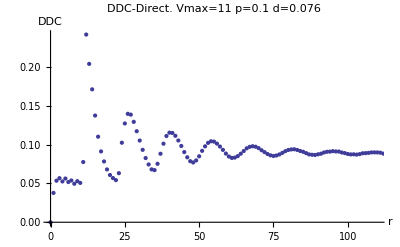

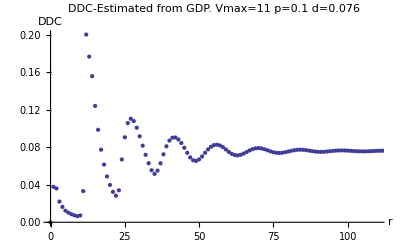

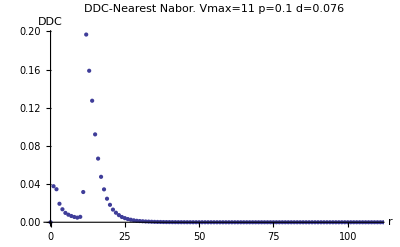

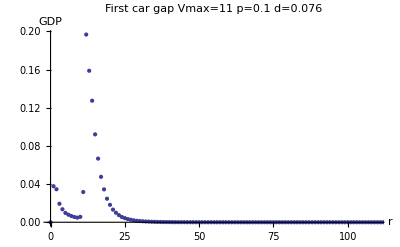

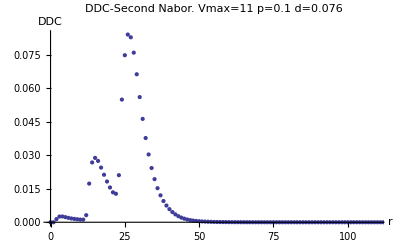

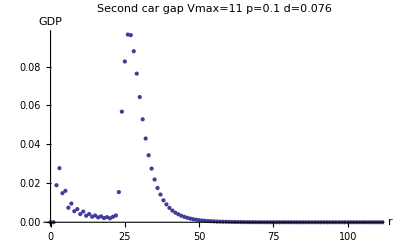

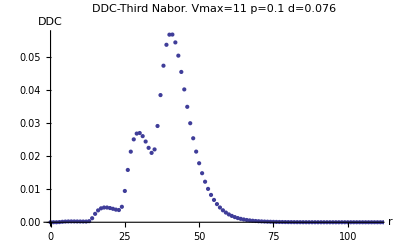

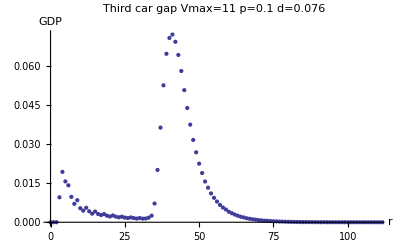

--------------------------------------------------------------------------------------

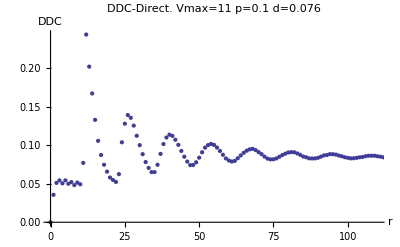

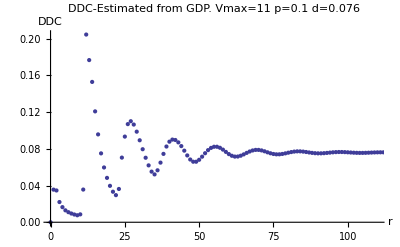

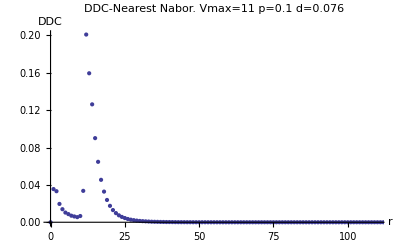

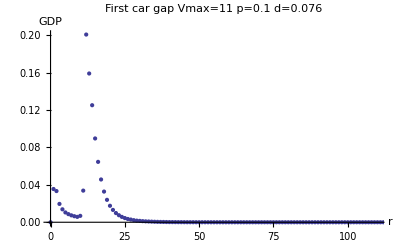

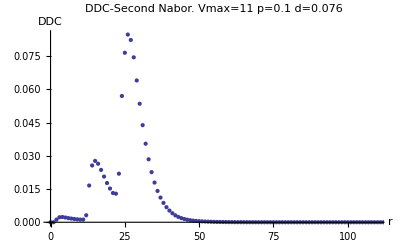

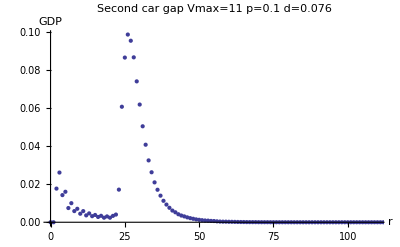

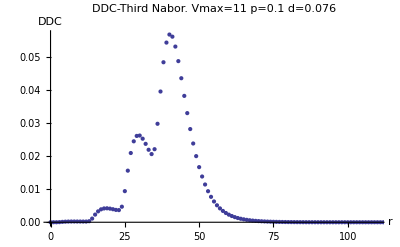

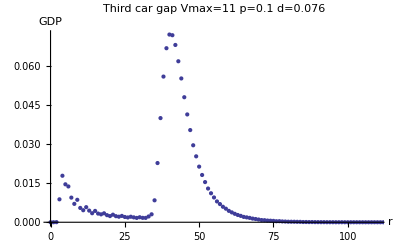

--------------------------------------------------------------------------------------

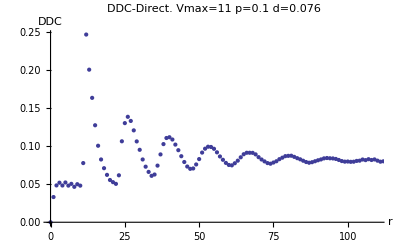

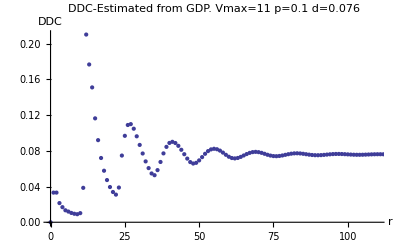

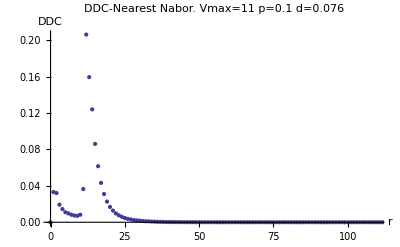

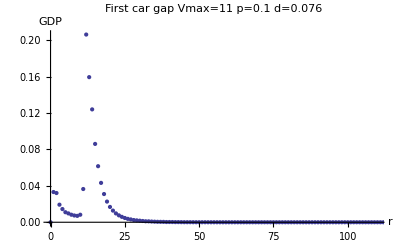

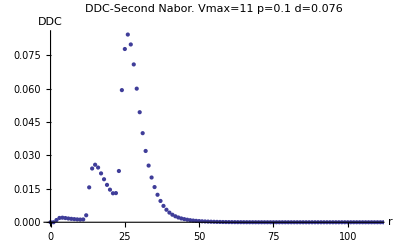

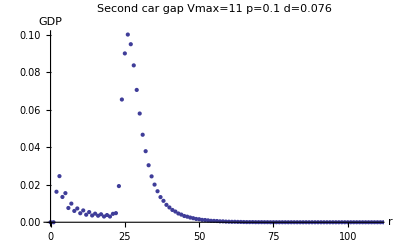

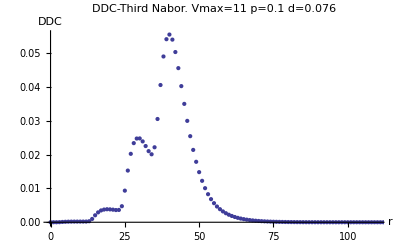

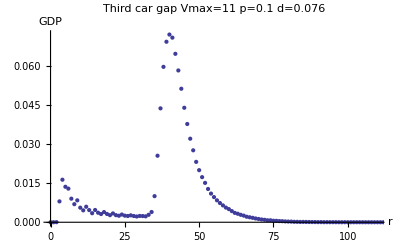

```mathematica
d="0.076";
p="0.1";
vmax="11";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated  vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]
"--------------------------------------------------------------------------------------"
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]

"--------------------------------------------------------------------------------------"
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs.  vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]
```

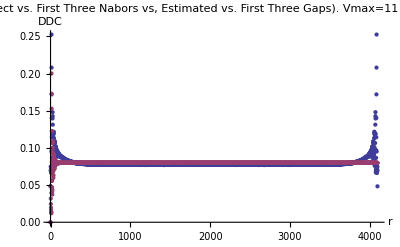

```mathematica
ListPlot[{DDC,DDCC},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
```

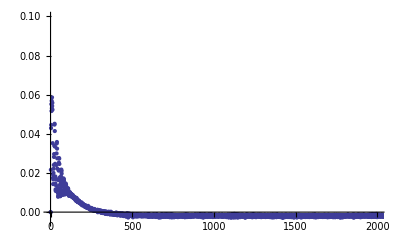

```mathematica
DDC2=DDC[[All,2]];
DDCC2=DDCC[[All,2]];
dif=Table[{i-1,DDC2[[i]]-DDCC2[[i]]},{i,1,4000}];
ListPlot[dif,PlotRange->{{0,2000},{-0.005,0.1}}]
```

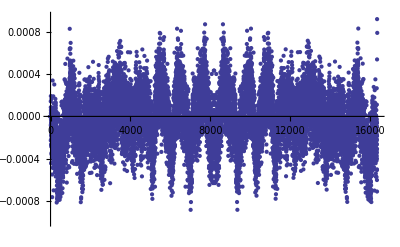

```mathematica
ListPlot[dif]
```

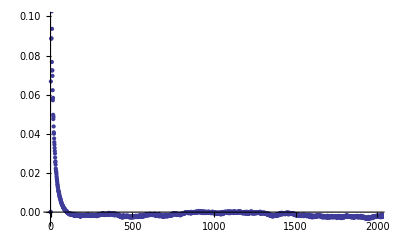

```mathematica
DDC2=DDC[[All,2]];
DDCC2=DDCC[[All,2]];
dif=Table[{i-1,DDC2[[i]]-DDCC2[[i]]},{i,1,4000}];
ListPlot[dif,PlotRange->{{0,2000},{-0.005,0.1}}]
```